### Full Generality

```mathematica
α = ({{α1}, {α2}});
c0=({{c01}, {c02}});
c1=({{c11}, {c12}});
β1=({{β11}, {β12}});
β2=({{β21}, {β22}});
A0=({{0, 0}, {A021, 0}}); (* A0=({{A011, A012, A013}, {A021, A022, A023}, {A031, A032, A033}}); *)
B0=({{0, 0}, {B021, 0}}); (* Subscript[B, 0]=({{B011, B012, B013}, {B021, B022, B023}, {B031, B032, B033}}); *)
H0=({{H01}, {H02}});
VU=({{U}, {U}});
e = ({{1}, {1}});
```

```mathematica
K1=IdentityMatrix[2] - μ h A0 ;
MatrixForm[K1 ]
```

(1 | 0
-A021 h μ | 1)

```mathematica
K2 = VU + B0 . e  σ (σ I10)/h;
MatrixForm[K2]
```

(U
U+1/2 B021 (W+Z/(√3)) σ^2)

```mathematica
H0= Inverse[K1].K2;
MatrixForm[H0]
```

(U
U+A021 h U μ+1/2 B021 (W+Z/(√3)) σ^2)

```mathematica
U2= U+ μ h αᵀ.H0 + σ I1 Transpose[e].β1+ σ I10/h Transpose[e].β2;
U2 =U2[[1]][[1]];
U2;
```

```mathematica
I10=1/2 h(W+Z/(√3)); 
I1= W;
```

```mathematica
U2Full = U2
```

U+W (β11+β12) σ+1/2 (W+Z/(√3)) (β21+β22) σ+h μ (U α1+α2 (U+A021 h U μ+1/2 B021 (W+Z/(√3)) σ^2))

```mathematica
U2Plugged = U2Full /.  {W -> 0,Z->0}
G = Coefficient[U2Plugged,U]
```

U+h μ (U α1+α2 (U+A021 h U μ))

1+h α1 μ+h α2 μ+A021 h^2 α2 μ^2

```mathematica
stableeq = G/.  {μ -> z/h}
```

1+z α1+z α2+A021 z^2 α2

```mathematica
1+z Transpose[α].Inverse[K1].e /.  {μ -> z/h}
```

{{1+z (α1+α2+A021 z α2)}}

Two Stage
A021 -> 1 to ensure c0[end] = 1
a1 + a2 = 1 -> a1 = 1-a2

```mathematica
Simplify[1+z α1+z α2+A021 z^2 α2]
```

1+A021 z^2 α2+z (α1+α2)

```mathematica
tsstab = Simplify[1+z α1+z α2-A021 z^2 α2 /. {A021->1,α1->1-α2}]
```

1+z-z^2 α2

```mathematica
Solve[1+z-z^2 α2 == 1,z]
Solve[1+z-z^2 α2 == -1,z]
```

{{z→0},{z→1/α2}}

{{z→(1-√(1+8 α2))/(2 α2)},{z→(1+√(1+8 α2))/(2 α2)}}

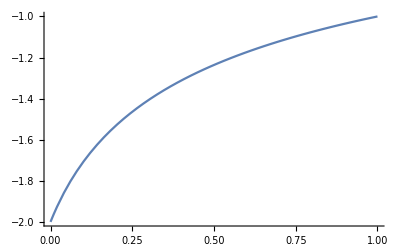

```mathematica
Val1[α2_]= (1+√(1+8 α2))/(2 α2);
Val2[α2_]= (1-√(1+8 α2))/(2 α2);
Plot[{Val2[α2]},{α2,0,1}]
```

```mathematica
zstab[α2_]:=(1-√(1+8 α2))/(2 α2)
```

```mathematica
Maximize[Val2,α2]
```

{Val2,{α2→0}}

```mathematica
cond1 = First[First[Transpose[α].e]] == 1;
cond2 = First[First[Transpose[β1].e]] == 1;
cond3 = First[First[Transpose[β2].e]] == 0;
cond4 = First[First[Transpose[α].B0.e]] == 1;
cond5 = First[First[Transpose[α].A0.e]] == 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] == 3/2;
cond7 = First[First[Transpose[β1].c1]] == 1;
cond8 = First[First[Transpose[β2].c1]] == -1;
vars = {α1,α2,c01,c02,c11,c12,β11,β12,β21,β22,A021,B021};
```

```mathematica
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,c02== 1,c12==1,c01==0,c11==0,A021==c02,B021== c12} ;
FindInstance[conds ,vars,Reals]
```

{}

```mathematica
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,A021==c02} ;
FindInstance[conds ,vars,Reals]
```

{{α1→1/3,α2→2/3,c01→42/5,c02→3/4,c11→0,c12→-1,β11→2,β12→-1,β21→-1,β22→1,A021→3/4,B021→3/2}}

```mathematica
Maximize[{(1-√(1+8 α2))/(2 α2),cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,c02== 1,c12==1,c01==0,c11==0,A021==c02} ,vars,Reals]
```

Maximize::infeas: There are no values of {α1, α2, c01, c02, c11, c12, β11, β12, β21, β22, A021, B021} for which the constraints α1 + α2 == 1 && β11 + β12 == 1 && β21 + β22 == 0 && B021\ α2 == 1 && A021\ α2 == 1/2 && B021^2\ α2 == 3/2 && c11\ β11 + c12\ β12 == 1 && c11\ β21 + c12\ β22 == -1 && c02 == 1 && c12 == 1 && c01 == 0 && c11 == 0 && A021 == c02 are satisfied and the objective function 1 - √1 + 8\ α2/2\ α2 is real valued.

{-∞,{α1→Indeterminate,α2→Indeterminate,c01→Indeterminate,c02→Indeterminate,c11→Indeterminate,c12→Indeterminate,β11→Indeterminate,β12→Indeterminate,β21→Indeterminate,β22→Indeterminate,A021→Indeterminate,B021→Indeterminate}}

```mathematica
Minimize[{(1-√(1+8 α2))/(2 α2),cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,c02== 1,c12==1,c01==0,c11==0,A021==c02} ,vars,Reals]
```

Minimize::infeas: There are no values of {α1, α2, c01, c02, c11, c12, β11, β12, β21, β22, A021, B021} for which the constraints α1 + α2 == 1 && β11 + β12 == 1 && β21 + β22 == 0 && B021\ α2 == 1 && A021\ α2 == 1/2 && B021^2\ α2 == 3/2 && c11\ β11 + c12\ β12 == 1 && c11\ β21 + c12\ β22 == -1 && c02 == 1 && c12 == 1 && c01 == 0 && c11 == 0 && A021 == c02 are satisfied and the objective function 1 - √1 + 8\ α2/2\ α2 is real valued.

{∞,{α1→Indeterminate,α2→Indeterminate,c01→Indeterminate,c02→Indeterminate,c11→Indeterminate,c12→Indeterminate,β11→Indeterminate,β12→Indeterminate,β21→Indeterminate,β22→Indeterminate,A021→Indeterminate,B021→Indeterminate}}

```mathematica
Maximize[{(1-√(1+8 α2))/(2 α2),cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,c02== 1,c12==1,0<c01<1,0<c11<1,A021==c02} ,vars,Reals]
```

Maximize::infeas: There are no values of {α1, α2, c01, c02, c11, c12, β11, β12, β21, β22, A021, B021} for which the constraints α1 + α2 == 1 && β11 + β12 == 1 && β21 + β22 == 0 && B021\ α2 == 1 && A021\ α2 == 1/2 && B021^2\ α2 == 3/2 && c11\ β11 + c12\ β12 == 1 && c11\ β21 + c12\ β22 == -1 && c02 == 1 && c12 == 1 && 0 < c01 < 1 && 0 < c11 < 1 && A021 == c02 are satisfied and the objective function 1 - √1 + 8\ α2/2\ α2 is real valued.

{-∞,{α1→Indeterminate,α2→Indeterminate,c01→Indeterminate,c02→Indeterminate,c11→Indeterminate,c12→Indeterminate,β11→Indeterminate,β12→Indeterminate,β21→Indeterminate,β22→Indeterminate,A021→Indeterminate,B021→Indeterminate}}

```mathematica
Minimize[{(1-√(1+8 α2))/(2 α2),cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,c02== 1,c12==1,0<c01<1,0<c11<1,A021==c02} ,vars,Reals]
```

Minimize::infeas: There are no values of {α1, α2, c01, c02, c11, c12, β11, β12, β21, β22, A021, B021} for which the constraints α1 + α2 == 1 && β11 + β12 == 1 && β21 + β22 == 0 && B021\ α2 == 1 && A021\ α2 == 1/2 && B021^2\ α2 == 3/2 && c11\ β11 + c12\ β12 == 1 && c11\ β21 + c12\ β22 == -1 && c02 == 1 && c12 == 1 && 0 < c01 < 1 && 0 < c11 < 1 && A021 == c02 are satisfied and the objective function 1 - √1 + 8\ α2/2\ α2 is real valued.

{∞,{α1→Indeterminate,α2→Indeterminate,c01→Indeterminate,c02→Indeterminate,c11→Indeterminate,c12→Indeterminate,β11→Indeterminate,β12→Indeterminate,β21→Indeterminate,β22→Indeterminate,A021→Indeterminate,B021→Indeterminate}}

```mathematica
Maximize[{(1-√(1+8 α2))/(2 α2),cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,c02== 1,0<c01<1,0<c11<1,A021==c02} ,vars,Reals]
```

Maximize::infeas: There are no values of {α1, α2, c01, c02, c11, c12, β11, β12, β21, β22, A021, B021} for which the constraints α1 + α2 == 1 && β11 + β12 == 1 && β21 + β22 == 0 && B021\ α2 == 1 && A021\ α2 == 1/2 && B021^2\ α2 == 3/2 && c11\ β11 + c12\ β12 == 1 && c11\ β21 + c12\ β22 == -1 && c02 == 1 && 0 < c01 < 1 && 0 < c11 < 1 && A021 == c02 are satisfied and the objective function 1 - √1 + 8\ α2/2\ α2 is real valued.

{-∞,{α1→Indeterminate,α2→Indeterminate,c01→Indeterminate,c02→Indeterminate,c11→Indeterminate,c12→Indeterminate,β11→Indeterminate,β12→Indeterminate,β21→Indeterminate,β22→Indeterminate,A021→Indeterminate,B021→Indeterminate}}

```mathematica
Maximize[{(1-√(1+8 α2))/(2 α2),cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,c01==0,0<c11<1,c11==0,A021==c02} ,vars,Reals]
```

Maximize::infeas: There are no values of {α1, α2, c01, c02, c11, c12, β11, β12, β21, β22, A021, B021} for which the constraints α1 + α2 == 1 && β11 + β12 == 1 && β21 + β22 == 0 && B021\ α2 == 1 && A021\ α2 == 1/2 && B021^2\ α2 == 3/2 && c11\ β11 + c12\ β12 == 1 && c11\ β21 + c12\ β22 == -1 && c01 == 0 && 0 < c11 < 1 && c11 == 0 && A021 == c02 are satisfied and the objective function 1 - √1 + 8\ α2/2\ α2 is real valued.

{-∞,{α1→Indeterminate,α2→Indeterminate,c01→Indeterminate,c02→Indeterminate,c11→Indeterminate,c12→Indeterminate,β11→Indeterminate,β12→Indeterminate,β21→Indeterminate,β22→Indeterminate,A021→Indeterminate,B021→Indeterminate}}

```mathematica
Maximize[{(1-√(1+8 α2))/(2 α2),cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,c01==0,0<c11<1,A021==c02} ,vars,Reals]
```

{3/4 (1-√(19/3)),{α2→2/3,A021→3/4,B021→3/2,c01→0,c02→3/4,c11→1/2,c12→0,α1→1/3,β11→2,β12→-1,β21→-2,β22→2}}

```mathematica
Minimize[{(1-√(1+8 α2))/(2 α2),cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,c01== 0,c02≥ 3/4,A021==c02} ,vars,Reals]
```

{3/4 (1-√(19/3)),{α2→2/3,A021→3/4,B021→3/2,c01→0,c02→3/4,c11→0,c12→-1,α1→1/3,β11→2,β12→-1,β21→-1,β22→1}}

```mathematica
Minimize[{(1-√(1+8 α2))/(2 α2),cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,A021==c02} ,vars,Reals]
```

{3/4 (1-√(19/3)),{α2→2/3,A021→3/4,B021→3/2,c01→42/5,c02→3/4,c11→0,c12→-1,α1→1/3,β11→2,β12→-1,β21→-1,β22→1}}

```mathematica
Maximize[{(1-√(1+8 α2))/(2 α2),cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,A021==c02} ,vars,Reals]
```

{3/4 (1-√(19/3)),{α2→2/3,A021→3/4,B021→3/2,c01→42/5,c02→3/4,c11→0,c12→-1,α1→1/3,β11→2,β12→-1,β21→-1,β22→1}}

```mathematica
N[3/4 (1-√(19/3))]
```

-1.13746

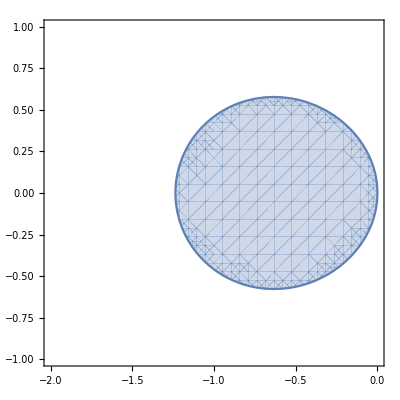

```mathematica
RegionPlot[Abs[1+z α1+z α2-A021 z^2 α2 /. {z-> x + ⅈ y,A021-> 3/4,α1->1/3,α2->2/3}]<1,{x,-2,0},{y,-1,1}]
```

```mathematica
RegionPlot[Abs[1+z α1+z α2-A021 z^2 α2 /. {z-> x + ⅈ y,A021-> 3/4,α1->1/3,α2->2/3}]<1,{x,-2,0},{y,-1,1}]
```

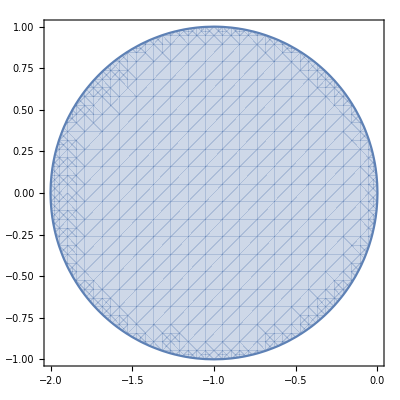

```mathematica
RegionPlot[Abs[1+z /.{z->x+I y}]<1,{x,-2,0},{y,-1,1}]
```

```mathematica
1+z α1+z α2-A021 z^2 α2 /. {z-> 0,A021-> 3/4,α1->1/3,α2->2/3}
```

1